```mathematica
f[x_,al_,be_]:=1/(1+1/al Exp[be x])
```

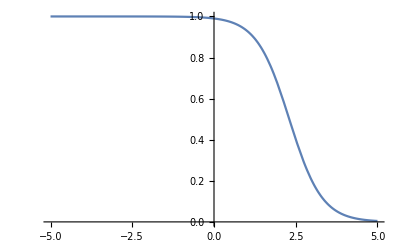

```mathematica
Plot[f[x,100,2],{x,-5,5}]
```

```mathematica
subs=FullSimplify[NSolve[{f[100,al,be]==99/100, f[600,al,be]==1/100},{al,be}, Reals]][[1]]
```

{al→622.142,be→0.0183805}

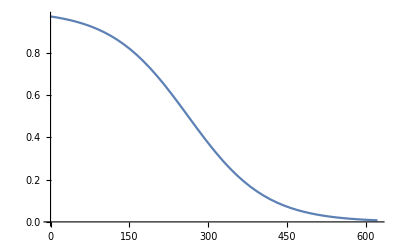

```mathematica
Plot[f[x,al,be]//.subs,{x,0,622}]
```

```mathematica
(* Check inverse transformation *)
```

```mathematica
xrestored=Simplify[Solve[f[x,al,be]==y,x,Reals],Assumptions->{y<1,y>0, al>0}][[1,1]]
```

x→Log[al (-1+1/y)]/be

```mathematica
xrestored//.(y->f[0.512312,al,be]//.subs)//.subs
```

x→0.512312